```mathematica
β11=0.1;
ϵ=0;
α1=22;
α2=30;
α3=200;
α4=8000;


Subscript[γ, 1]=(√((0*α*ξ)+k^2));
Subscript[γ, 2]=√((α1*ξ^2)+k^2);
Subscript[γ, 31]=Subscript[γ, 1]*β11;
Subscript[γ, 41]=Subscript[γ, 2]*β11;

Subscript[γ, 22]=√((α2*ξ^2)+k^2);
Subscript[γ, 32]=Subscript[γ, 1]*β11;
Subscript[γ, 42]=Subscript[γ, 22]*β11;

Subscript[γ, 23]=√((α3*ξ^2)+k^2);
Subscript[γ, 33]=Subscript[γ, 1]*β11;
Subscript[γ, 43]=Subscript[γ, 23]*β11;

Subscript[γ, 24]=√((α4*ξ^2)+k^2);
Subscript[γ, 34]=Subscript[γ, 1]*β11;
Subscript[γ, 44]=Subscript[γ, 24]*β11;

Subscript[γ, 25]=√((α5*ξ^2)+k^2);
Subscript[γ, 35]=Subscript[γ, 1]*β11;
Subscript[γ, 45]=Subscript[γ, 25]*β11;

Subscript[γ, 26]=√((α6*ξ^2)+k^2);
Subscript[γ, 36]=Subscript[γ, 1]*β11;
Subscript[γ, 46]=Subscript[γ, 26]*β11;

Subscript[γ, 27]=√((α7*ξ^2)+k^2);
Subscript[γ, 37]=Subscript[γ, 1]*β11;
Subscript[γ, 47]=Subscript[γ, 27]*β11;


p1=ContourPlot[{{(Det[{{(0.5*(Subscript[γ, 2]^2+k^2)*BesselI[0,Subscript[γ, 1]])-(Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]])-(0.5*α1*(1-k^2)*Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]]),(-ⅈ*k*Subscript[γ, 2]*BesselI[0,Subscript[γ, 2]])+(ⅈ*k*BesselI[1,Subscript[γ, 2]])+(0.5*α1*ⅈ*k*(1-k^2)*BesselI[1,Subscript[γ, 2]]),(0.5*(Subscript[γ, 2]^2+k^2)*BesselK[0,Subscript[γ, 1]])+(Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]])+(0.5*α1*(1-k^2)*Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]]),(ⅈ*k*Subscript[γ, 2]*BesselK[0,Subscript[γ, 2]])+(ⅈ*k*BesselK[1,Subscript[γ, 2]])+(0.5*α1*ⅈ*k*(1-k^2)*BesselK[1,Subscript[γ, 2]])},{2.0*Subscript[γ, 1]*ⅈ*k*BesselI[1,Subscript[γ, 1]],(k^2+Subscript[γ, 2]^2)*BesselI[1,Subscript[γ, 2]],-2.0*Subscript[γ, 1]*ⅈ*k*BesselK[1,Subscript[γ, 1]],(k^2+Subscript[γ, 2]^2)*BesselK[1,Subscript[γ, 2]]},{Subscript[γ, 1]*BesselI[1,Subscript[γ, 31]],-ⅈ*k*BesselI[1,Subscript[γ, 41]],-Subscript[γ, 1]*BesselK[1,Subscript[γ, 31]],-ⅈ*k*BesselK[1,Subscript[γ, 41]]},{(ⅈ*k*ϵ*Subscript[γ, 1]*BesselI[1,Subscript[γ, 31]])-(ⅈ*k*BesselI[0,Subscript[γ, 31]]),(Subscript[γ, 2]^2*ϵ*BesselI[1,Subscript[γ, 41]])-(Subscript[γ, 2]*BesselI[0,Subscript[γ, 41]]),-(ⅈ*k*ϵ*Subscript[γ, 1]*BesselK[1,Subscript[γ, 31]])-(ⅈ*k*BesselK[0,Subscript[γ, 31]]),(Subscript[γ, 2]^2*ϵ*BesselK[1,Subscript[γ, 41]])+(Subscript[γ, 2]*BesselK[0,Subscript[γ, 41]])}}])==0},{(Det[{{(0.5*(Subscript[γ, 22]^2+k^2)*BesselI[0,Subscript[γ, 1]])-(Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]])-(0.5*α2*(1-k^2)*Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]]),(-ⅈ*k*Subscript[γ, 22]*BesselI[0,Subscript[γ, 22]])+(ⅈ*k*BesselI[1,Subscript[γ, 22]])+(0.5*α2*ⅈ*k*(1-k^2)*BesselI[1,Subscript[γ, 22]]),(0.5*(Subscript[γ, 22]^2+k^2)*BesselK[0,Subscript[γ, 1]])+(Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]])+(0.5*α2*(1-k^2)*Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]]),(ⅈ*k*Subscript[γ, 22]*BesselK[0,Subscript[γ, 22]])+(ⅈ*k*BesselK[1,Subscript[γ, 22]])+(0.5*α2*ⅈ*k*(1-k^2)*BesselK[1,Subscript[γ, 22]])},{2.0*Subscript[γ, 1]*ⅈ*k*BesselI[1,Subscript[γ, 1]],(k^2+Subscript[γ, 22]^2)*BesselI[1,Subscript[γ, 22]],-2.0*Subscript[γ, 1]*ⅈ*k*BesselK[1,Subscript[γ, 1]],(k^2+Subscript[γ, 22]^2)*BesselK[1,Subscript[γ, 22]]},{Subscript[γ, 1]*BesselI[1,Subscript[γ, 32]],-ⅈ*k*BesselI[1,Subscript[γ, 42]],-Subscript[γ, 1]*BesselK[1,Subscript[γ, 32]],-ⅈ*k*BesselK[1,Subscript[γ, 42]]},{(ⅈ*k*ϵ*Subscript[γ, 1]*BesselI[1,Subscript[γ, 32]])-(ⅈ*k*BesselI[0,Subscript[γ, 32]]),(Subscript[γ, 22]^2*ϵ*BesselI[1,Subscript[γ, 42]])-(Subscript[γ, 22]*BesselI[0,Subscript[γ, 42]]),-(ⅈ*k*ϵ*Subscript[γ, 1]*BesselK[1,Subscript[γ, 32]])-(ⅈ*k*BesselK[0,Subscript[γ, 32]]),(Subscript[γ, 22]^2*ϵ*BesselK[1,Subscript[γ, 42]])+(Subscript[γ, 22]*BesselK[0,Subscript[γ, 42]])}}])==0}, {(Det[{{(0.5*(Subscript[γ, 23]^2+k^2)*BesselI[0,Subscript[γ, 1]])-(Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]])-(0.5*α3*(1-k^2)*Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]]),(-ⅈ*k*Subscript[γ, 23]*BesselI[0,Subscript[γ, 23]])+(ⅈ*k*BesselI[1,Subscript[γ, 23]])+(0.5*α3*ⅈ*k*(1-k^2)*BesselI[1,Subscript[γ, 23]]),(0.5*(Subscript[γ, 23]^2+k^2)*BesselK[0,Subscript[γ, 1]])+(Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]])+(0.5*α3*(1-k^2)*Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]]),(ⅈ*k*Subscript[γ, 23]*BesselK[0,Subscript[γ, 23]])+(ⅈ*k*BesselK[1,Subscript[γ, 23]])+(0.5*α3*ⅈ*k*(1-k^2)*BesselK[1,Subscript[γ, 23]])},{2.0*Subscript[γ, 1]*ⅈ*k*BesselI[1,Subscript[γ, 1]],(k^2+Subscript[γ, 23]^2)*BesselI[1,Subscript[γ, 23]],-2.0*Subscript[γ, 1]*ⅈ*k*BesselK[1,Subscript[γ, 1]],(k^2+Subscript[γ, 23]^2)*BesselK[1,Subscript[γ, 23]]},{Subscript[γ, 1]*BesselI[1,Subscript[γ, 33]],-ⅈ*k*BesselI[1,Subscript[γ, 43]],-Subscript[γ, 1]*BesselK[1,Subscript[γ, 33]],-ⅈ*k*BesselK[1,Subscript[γ, 43]]},{(ⅈ*k*ϵ*Subscript[γ, 1]*BesselI[1,Subscript[γ, 33]])-(ⅈ*k*BesselI[0,Subscript[γ, 33]]),(Subscript[γ, 23]^2*ϵ*BesselI[1,Subscript[γ, 43]])-(Subscript[γ, 23]*BesselI[0,Subscript[γ, 43]]),-(ⅈ*k*ϵ*Subscript[γ, 1]*BesselK[1,Subscript[γ, 33]])-(ⅈ*k*BesselK[0,Subscript[γ, 33]]),(Subscript[γ, 23]^2*ϵ*BesselK[1,Subscript[γ, 43]])+(Subscript[γ, 23]*BesselK[0,Subscript[γ, 43]])}}])==0}, {(Det[{{(0.5*(Subscript[γ, 24]^2+k^2)*BesselI[0,Subscript[γ, 1]])-(Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]])-(0.5*α4*(1-k^2)*Subscript[γ, 1]*BesselI[1,Subscript[γ, 1]]),(-ⅈ*k*Subscript[γ, 24]*BesselI[0,Subscript[γ, 24]])+(ⅈ*k*BesselI[1,Subscript[γ, 24]])+(0.5*α4*ⅈ*k*(1-k^2)*BesselI[1,Subscript[γ, 24]]),(0.5*(Subscript[γ, 24]^2+k^2)*BesselK[0,Subscript[γ, 1]])+(Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]])+(0.5*α4*(1-k^2)*Subscript[γ, 1]*BesselK[1,Subscript[γ, 1]]),(ⅈ*k*Subscript[γ, 24]*BesselK[0,Subscript[γ, 24]])+(ⅈ*k*BesselK[1,Subscript[γ, 24]])+(0.5*α4*ⅈ*k*(1-k^2)*BesselK[1,Subscript[γ, 24]])},{2.0*Subscript[γ, 1]*ⅈ*k*BesselI[1,Subscript[γ, 1]],(k^2+Subscript[γ, 24]^2)*BesselI[1,Subscript[γ, 24]],-2.0*Subscript[γ, 1]*ⅈ*k*BesselK[1,Subscript[γ, 1]],(k^2+Subscript[γ, 24]^2)*BesselK[1,Subscript[γ, 24]]},{Subscript[γ, 1]*BesselI[1,Subscript[γ, 34]],-ⅈ*k*BesselI[1,Subscript[γ, 44]],-Subscript[γ, 1]*BesselK[1,Subscript[γ, 34]],-ⅈ*k*BesselK[1,Subscript[γ, 44]]},{(ⅈ*k*ϵ*Subscript[γ, 1]*BesselI[1,Subscript[γ, 34]])-(ⅈ*k*BesselI[0,Subscript[γ, 34]]),(Subscript[γ, 24]^2*ϵ*BesselI[1,Subscript[γ, 44]])-(Subscript[γ, 24]*BesselI[0,Subscript[γ, 44]]),-(ⅈ*k*ϵ*Subscript[γ, 1]*BesselK[1,Subscript[γ, 34]])-(ⅈ*k*BesselK[0,Subscript[γ, 34]]),(Subscript[γ, 24]^2*ϵ*BesselK[1,Subscript[γ, 44]])+(Subscript[γ, 24]*BesselK[0,Subscript[γ, 44]])}}])==0}}, {k,0.0001,1},{ξ,0.0000001,0.4},

Frame->True,FrameLabel->{{HoldForm["s̄"],None},{HoldForm[k̄],None}},FrameStyle->Directive[Thick,Black,(FontSize->20), FontFamily->"Times"],    ContourStyle->{Black,Directive[Dashed,Blue],Directive[Dotted,Red], Green},AxesStyle->AbsoluteThickness[5],PlotLegends->Placed[LineLegend[{"Σ=22","Σ=30","Σ=200","Σ=8000"},LegendLayout->{"Column",1},LegendMarkerSize->16],{Left,0.9},Pane[#,450,Alignment->Left]&], MaxRecursion->6,PlotRange->Full]
```

Det::luc: Result for Det of badly conditioned matrix {{-1.37884×10^-7+0. ⅈ,0.+1.86744×10^-7 ⅈ,12.+0. ⅈ,0.+9.44136 ⅈ},{0.+5.03727×10^-12 ⅈ,8.37255×10^-12+0. ⅈ,0.-0.000342843 ⅈ,0.000352748+0. ⅈ},{1.46927×10^-9+0. ⅈ,0.-1.86744×10^-9 ⅈ,-10.+0. ⅈ,0.-7.86781 ⅈ},{0.-0.000171421 ⅈ,-0.000217877+0. ⅈ,0.-0.00190105 ⅈ,0.00236399+0. ⅈ}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{-1.93366×10^-7+0. ⅈ,0.+2.78964×10^-7 ⅈ,16.+0. ⅈ,0.+11.7978 ⅈ},{0.+5.03727×10^-12 ⅈ,9.69814×10^-12+0. ⅈ,0.-0.000342843 ⅈ,0.000358879+0. ⅈ},{1.46927×10^-9+0. ⅈ,0.-1.9926×10^-9 ⅈ,-10.+0. ⅈ,0.-7.37361 ⅈ},{0.-0.000171421 ⅈ,-0.00023248+0. ⅈ,0.-0.00190105 ⅈ,0.00250735+0. ⅈ}} may contain significant numerical errors.

Det::luc: Result for Det of badly conditioned matrix {{-1.37237×10^-6+0. ⅈ,0.+3.73544×10^-6 ⅈ,101.+0. ⅈ,0.+39.3291 ⅈ},{0.+5.03727×10^-12 ⅈ,4.91245×10^-11+0. ⅈ,0.-0.000342843 ⅈ,0.000506973+0. ⅈ},{1.46927×10^-9+0. ⅈ,0.-3.77317×10^-9 ⅈ,-10.+0. ⅈ,0.-3.89398 ⅈ},{0.-0.000171421 ⅈ,-0.000440222+0. ⅈ,0.-0.00190105 ⅈ,0.00446682+0. ⅈ}} may contain significant numerical errors.

General::stop: Further output of Det::luc will be suppressed during this calculation.

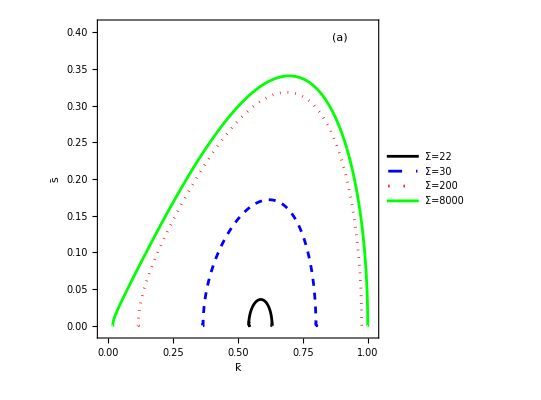

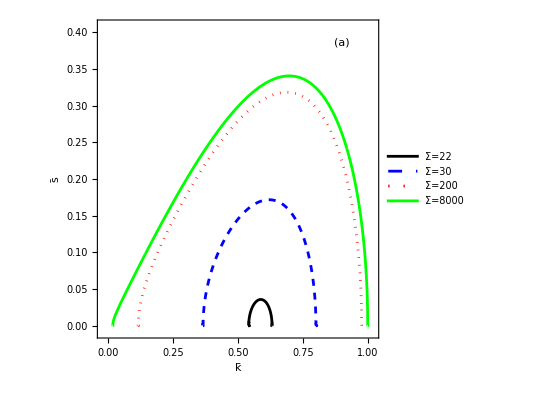

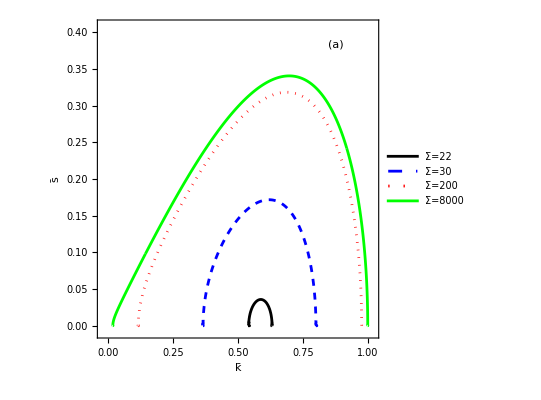

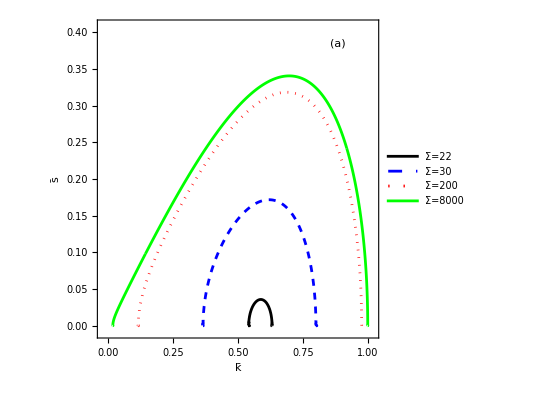

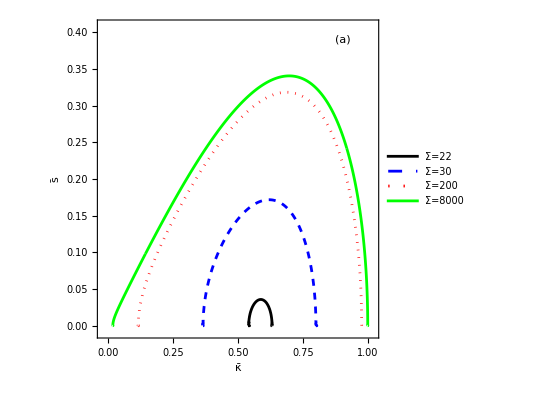

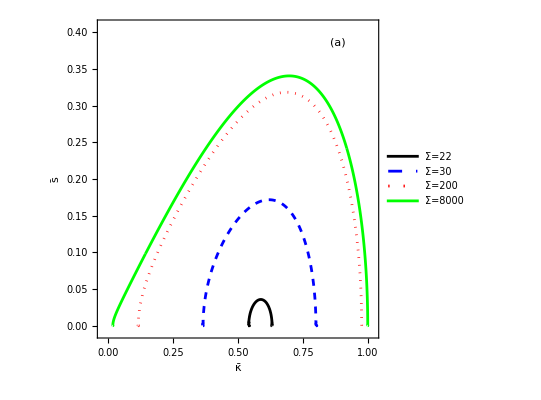

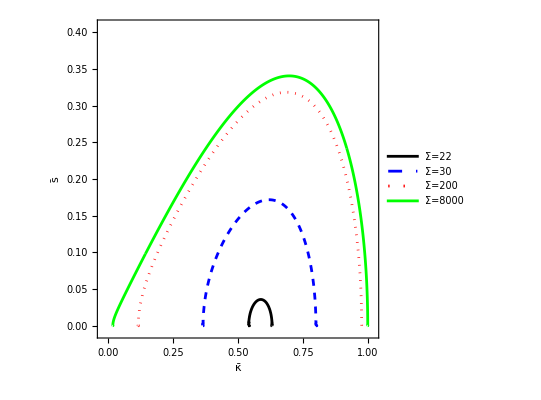

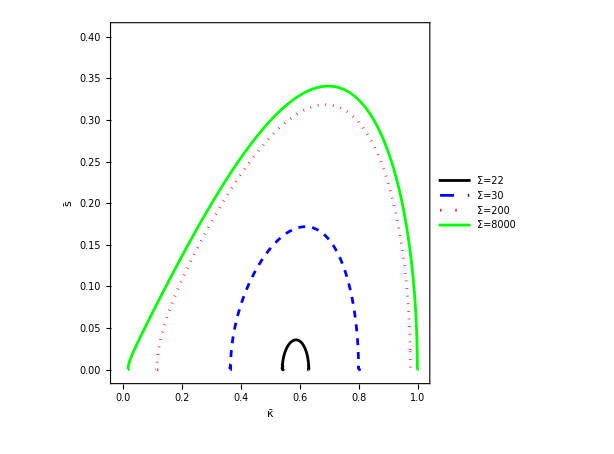
```mathematica
-Graphics-^□
```

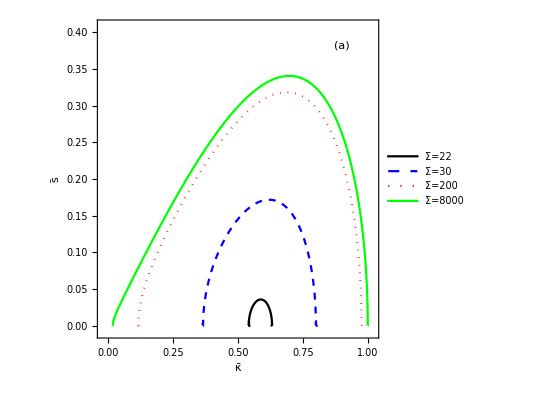

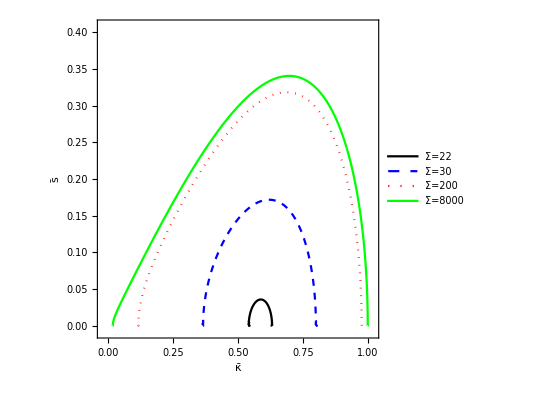

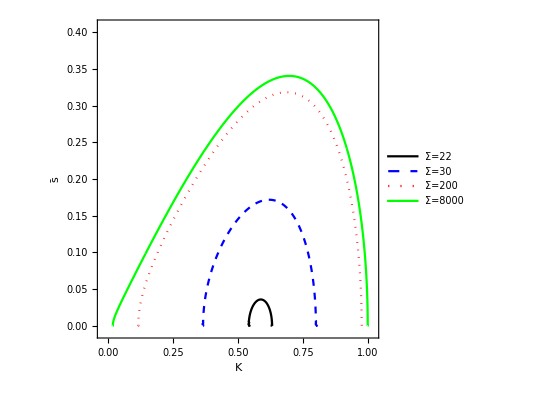

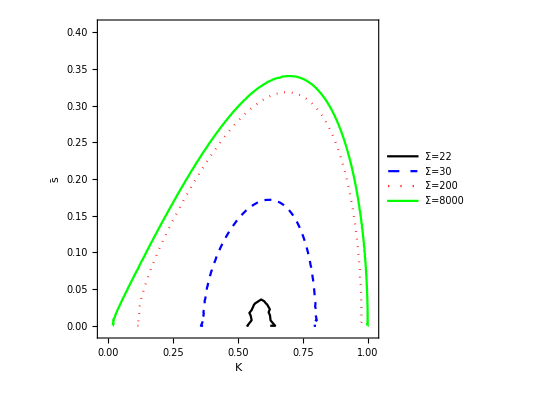

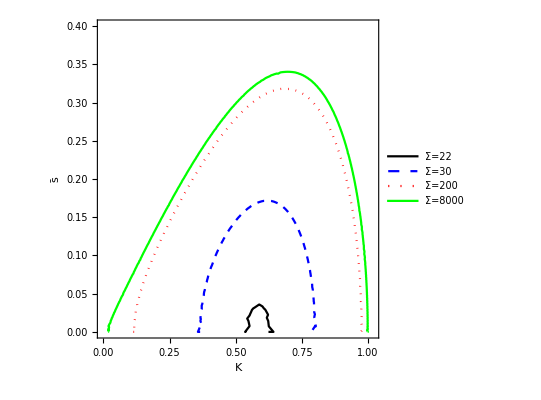

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```

```mathematica
SystemOpen["exportP1.pdf"]
```